## Single Pendulum

```mathematica
l = 1; tmax = 20; g = 9.8; w = l/g;
```

```mathematica
SinglePendulum[w_, pDot0_, tmax_] :=   NDSolve[{Sin[p[t]]+ w p''[t]==0, p[0]==0, p'[0]== pDot0}, p, {t, 0, tmax}];
```

```mathematica
s = p[t] /. SinglePendulum[w , 1.0, tmax]
```

{InterpolatingFunction[{{0., 20.}}, <>][t]}

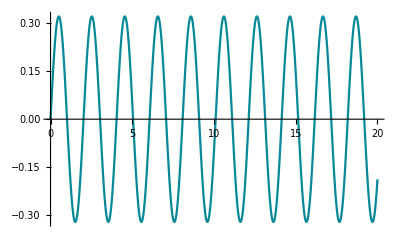

```mathematica
Plot[s,{t,0,tmax},PlotRange->All]
```

```mathematica
c={l Cos[p[t]],l Sin[p[t]]}/.SinglePendulum[w,w0,tmax]
```

{{Cos[InterpolatingFunction[{{0., 20.}}, <>][t]],Sin[InterpolatingFunction[{{0., 20.}}, <>][t]]}}